```mathematica
a = Sqrt[3/2* 5];
Subscript[α, g]=1/50;
Subscript[α, l]=1/120;
H = 1/2;
```

```mathematica
F[x_,s_] := (Subscript[α, g]+Subscript[α, l])/(Subscript[α, l]+Subscript[α, g]*Exp[-(Subscript[α, g]+Subscript[α, l])*s])*(Sqrt[((Subscript[α, g]*Subscript[α, l]*(1-x)*s^2)/x)]*Exp[-Subscript[α, g]*(1-x)*s - Subscript[α, l]*x*s]*BesselI[1,2*Sqrt[Subscript[α, g]*Subscript[α, l]*x*(1-x)*s^2]])
F0[s_]:=(Subscript[α, g]+Subscript[α, l])/(Subscript[α, l]+Subscript[α, g]*Exp[-(Subscript[α, g]+Subscript[α, l])*s])*Exp[-Subscript[α, g]*s]
g[s_]:=Subscript[α, l]/(Subscript[α, g]+Subscript[α, l])+Subscript[α, g]/(Subscript[α, g]+Subscript[α, l])*Exp[-(Subscript[α, g]+Subscript[α, l])*s]
ρ[L_]:=Subscript[α, l]*Exp[-L*Subscript[α, l]]

Subscript[π, g]:=Subscript[α, l]/(Subscript[α, g]+Subscript[α, l])
Subscript[π, l]:=Subscript[α, g]/(Subscript[α, g]+Subscript[α, l])
wa1[x_,s_]:=Subscript[π, g]*g[s]*F[x,s]
wa0[s_]:=Subscript[π, g]*g[s]*F0[s]
wb1[l1_,l2_,x_,s_]:=2*Subscript[π, l]*ρ[l1]*ρ[l2]*g[s-l2]*F[x,s-l2]
wb0[l1_,l2_,s_]:=2*Subscript[π, l]*ρ[l1]*ρ[l2]*g[s-l2]*F0[s-l2]
wc[l1_,l2_,s_]:=Subscript[π, l]*ρ[l1]*ρ[l2]
wd1[l1_,l2_,h_,x_,L_,s_]:=Subscript[π, l]*ρ[l1]*ρ[l2]*ρ[L]*Subscript[α, g]*g[h]*F[x,h]
wd0[l1_,l2_,h_,L_,s_]:=Subscript[π, l]*ρ[l1]*ρ[l2]*ρ[L]*Subscript[α, g]*g[h]*F0[h]

Subscript[σ, f][s_]:=s^(2*H)
Subscript[σ, b][s_,L_]:=Subscript[σ, f][s]*(1-(Subscript[σ, f][L]+Subscript[σ, f][s]-Subscript[σ, f][L-s])^2/(4*Subscript[σ, f][s]*Subscript[σ, f][L]))
P[σ_,R_]:=1/(2*π*σ/3)^(3/2)*Exp[-3*R^2/(2*σ)]
K[R_]:=Exp[-3*R^2/(2*a^2)]

Pa[x_,s_,R_]:=P[Subscript[σ, f][s*(1-x)],R]
Pb[l1_,l2_,x_,s_,R_]:=P[Subscript[σ, b][l2,l1+l2]+Subscript[σ, f][(1-x)*(s-l2)],R]
Pc[l1_,l2_,s_,R_]:=P[Subscript[σ, b][s,l1+l2],R]
Pd[l1_,l2_,h_,x_,L_,s_,R_]:=P[Subscript[σ, b][l2,l1+l2]+Subscript[σ, f][(1-x)*h]+Subscript[σ, b][s-h-l2,L],R]

Wa1[s_] := NIntegrate[wa1[x,s],{x,0,1}]
Wa0[s_]:=wa0[s]
Wa[s_]:=Wa1[s]+Wa0[s]
Wb1[s_]:=NIntegrate[wb1[l1,l2,x,s],{x,0,1},{l1,0,∞},{l2,0,s}]
Wb0[s_]:=NIntegrate[wb0[l1,l2,s],{l1,0,∞},{l2,0,s}]
Wb[s_]:=Wb1[s]+Wb0[s]
Wc[s_]:=NIntegrate[wc[l1,l2,s],{l1,0,∞},{l2,s,∞}]
Wd1[s_]:=NIntegrate[wd1[l1,l2,h,x,L,s],{l1,0,∞},{l2,0,s},{h,0,s-l2},{L,s-l2-h,∞},{x,0,1}]
Wd0[s_]:=NIntegrate[wd0[l1,l2,h,L,s],{l1,0,∞},{l2,0,s},{h,0,s-l2},{L,s-l2-h,∞}]
Wd[s_]:=Wd1[s]+Wd0[s]

PNloops[s1_,s2_]:=((s1*s2)^(2H)-0.25*((s1+s2)^(2H)-(s1)^(2H)-(s2)^(2H))^2)^(-3/2)
PNloopsSingle[s_]:=(s^(2H))^(-3/2)
```

```mathematica
Ra[s_]:=4*π*(NIntegrate[wa1[x,s]*Pa[x,s,R]*K[R]*R^2,{R,0,∞},{x,0,1}]+NIntegrate[wa0[s]*Pa[0,s,R]*K[R]*R^2,{R,0,∞}])
Rb[s_]:=4*π*(NIntegrate[wb1[l1,l2,x,s]*Pb[l1,l2,x,s,R]*K[R]*R^2,{R,0,∞},{x,0,1},{l1,0,∞},{l2,0,s}]+NIntegrate[wb0[l1,l2,s]*Pb[l1,l2,0,s,R]*K[R]*R^2,{R,0,∞},{l1,0,∞},{l2,0,s}])
Rc[s_]:=4*π*(NIntegrate[wc[l1,l2,s]*Pc[l1,l2,s,R]*K[R]*R^2,{R,0,∞},{l1,0.000000001,∞},{l2,s,∞}])
Rd[s_]:=4*π*(NIntegrate[wd1[l1,l2,h,x,L,s]*Pd[l1,l2,h,x,L,s,R]*K[R]*R^2,{R,0,∞},{l1,0,∞},{l2,0,s},{h,0,s-l2},{L,s-l2-h,∞},{x,0,1}] + NIntegrate[wd0[l1,l2,h,L,s]*Pd[l1,l2,h,0,L,s,R]*K[R]*R^2,{R,0,∞},{l1,0,∞},{l2,0,s},{h,0,s-l2},{L,s-l2-h,∞}])
R[s_]:=Ra[s]+Rb[s]+Rc[s]+Rd[s]
```

```mathematica
Smin=10^3;
Smax = 5*10^3;

Ns=5
q=(Smax/Smin)^(1/(Ns-1));
```

5

```mathematica
ContactFPFractal=Table[{Smin×q^(n-1),R[Smin×q^(n-1)]},{n,Ns}]
```

```mathematica
ContactFPFractal={{1,0.829676},{2^(3/49) 5^(4/49),0.802952},{2^(6/49) 5^(8/49),0.773047},{2^(9/49) 5^(12/49),0.739903},{2^(12/49) 5^(16/49),0.703568},{2^(15/49) 5^(20/49),0.664214},{2^(18/49) 5^(24/49),0.622158},{2^(3/7) 5^(4/7),0.577861},{2^(24/49) 5^(32/49),0.531932},{2^(27/49) 5^(36/49),0.4851},{2^(30/49) 5^(40/49),0.438177},{2^(33/49) 5^(44/49),0.39201},{2^(36/49) 5^(48/49),0.34742},{5 2^(39/49) 5^(3/49),0.30515},{5 2^(6/7) 5^(1/7),0.26581},{5 2^(45/49) 5^(11/49),0.229851},{5 2^(48/49) 5^(15/49),0.197542},{10 2^(2/49) 5^(19/49),0.168981},{10 2^(5/49) 5^(23/49),0.144109},{10 2^(8/49) 5^(27/49),0.122739},{10 2^(11/49) 5^(31/49),0.104591},{10 2^(2/7) 5^(5/7),0.0893272},{10 2^(17/49) 5^(39/49),0.076579},{10 2^(20/49) 5^(43/49),0.0659732},{10 2^(23/49) 5^(47/49),0.0571512},{50 2^(26/49) 5^(2/49),0.0497813},{50 2^(29/49) 5^(6/49),0.0435678},{50 2^(32/49) 5^(10/49),0.0382559},{50 2^(5/7) 5^(2/7),0.0336338},{50 2^(38/49) 5^(18/49),0.0295338},{50 2^(41/49) 5^(22/49),0.0258305},{50 2^(44/49) 5^(26/49),0.0224389},{50 2^(47/49) 5^(30/49),0.01931},{100 2^(1/49) 5^(34/49),0.0164239},{100 2^(4/49) 5^(38/49),0.0137835},{100 2^(1/7) 5^(6/7),0.0114031},{100 2^(10/49) 5^(46/49),0.00929958},{500 2^(13/49) 5^(1/49),0.00748331},{500 2^(16/49) 5^(5/49),0.00595212},{500 2^(19/49) 5^(9/49),0.00469012},{500 2^(22/49) 5^(13/49),0.00366981},{500 2^(25/49) 5^(17/49),0.0028573},{500 2^(4/7) 5^(3/7),0.00221746},{500 2^(31/49) 5^(25/49),0.0017171},{500 2^(34/49) 5^(29/49),0.00132767},{500 2^(37/49) 5^(33/49),0.00102512},{500 2^(40/49) 5^(37/49),0.000791353},{500 2^(43/49) 5^(41/49),0.000610492},{500 2^(46/49) 5^(45/49),0.000470867},{5000,0.000363037}};
```

```mathematica
logDerivative1=Table[{(ContactFPFractal[[i,1]]+ContactFPFractal[[i+1,1]])/2*10^3,Log[ContactFPFractal[[i+1,2]]/ContactFPFractal[[i,2]]]/Log[ContactFPFractal[[i+1,1]]/ContactFPFractal[[i,1]]]},{i,1,Length[ContactFPFractal]-1}];
```

```mathematica
Ra[s_]:=4/3*π*a^3*NIntegrate[wa1[x,s]*Pa[x,s,0],{x,0,1}]+wa0[s]*Pa[0,s,0]
Rb[s_]:=4/3*π*a^3*(NIntegrate[wb1[l1,l2,x,s]*Pb[l1,l2,x,s,0],{x,0,1},{l1,0,∞},{l2,0,s}]+NIntegrate[wb0[l1,l2,s]*Pb[l1,l2,0,s,0],{l1,0,∞},{l2,0,s}])
Rc[s_]:=4/3*π*a^3*(NIntegrate[wc[l1,l2,s]*Pc[l1,l2,s,0],{l1,0.000000001,∞},{l2,s,∞}])
Rd[s_]:=4/3*π*a^3*(NIntegrate[wd1[l1,l2,h,x,L,s]*Pd[l1,l2,h,x,L,s,0],{l1,0,∞},{l2,0,s},{h,0,s-l2},{L,s-l2-h,∞},{x,0,1}] + NIntegrate[wd0[l1,l2,h,L,s]*Pd[l1,l2,h,0,L,s,0],{l1,0,∞},{l2,0,s},{h,0,s-l2},{L,s-l2-h,∞}])
R[s_]:=Ra[s]+Rb[s]+Rc[s]+Rd[s]
```

```mathematica
Smin=1;
Smax = 5 * 10^3;

Ns=50;
q=(Smax/Smin)^(1/(Ns-1));
```

```mathematica
ContactNoCutoff=Table[{Smin×q^(n-1),R[Smin×q^(n-1)]},{n,Ns}];
```

```mathematica
ContactNoCutoff ={{1,20.5626},{2^(3/49) 5^(4/49),15.908},{2^(6/49) 5^(8/49),12.3168},{2^(9/49) 5^(12/49),9.54543},{2^(12/49) 5^(16/49),7.40612},{2^(15/49) 5^(20/49),5.75416},{2^(18/49) 5^(24/49),4.47804},{2^(3/7) 5^(4/7),3.49179},{2^(24/49) 5^(32/49),2.72916},{2^(27/49) 5^(36/49),2.13907},{2^(30/49) 5^(40/49),1.68215},{2^(33/49) 5^(44/49),1.32804},{2^(36/49) 5^(48/49),1.05331},{5 2^(39/49) 5^(3/49),0.839916},{5 2^(6/7) 5^(1/7),0.673903},{5 2^(45/49) 5^(11/49),0.544515},{5 2^(48/49) 5^(15/49),0.443436},{10 2^(2/49) 5^(19/49),0.364241},{10 2^(5/49) 5^(23/49),0.301955},{10 2^(8/49) 5^(27/49),0.252725},{10 2^(11/49) 5^(31/49),0.213562},{10 2^(2/7) 5^(5/7),0.182144},{10 2^(17/49) 5^(39/49),0.156664},{10 2^(20/49) 5^(43/49),0.135718},{10 2^(23/49) 5^(47/49),0.118216},{50 2^(26/49) 5^(2/49),0.103318},{50 2^(29/49) 5^(6/49),0.0903807},{50 2^(32/49) 5^(10/49),0.0789285},{50 2^(5/7) 5^(2/7),0.0686195},{50 2^(38/49) 5^(18/49),0.0592267},{50 2^(41/49) 5^(22/49),0.0506175},{50 2^(44/49) 5^(26/49),0.0427357},{50 2^(47/49) 5^(30/49),0.0355794},{100 2^(1/49) 5^(34/49),0.0291787},{100 2^(4/49) 5^(38/49),0.0235702},{100 2^(1/7) 5^(6/7),0.0187738},{100 2^(10/49) 5^(46/49),0.0147765},{500 2^(13/49) 5^(1/49),0.011526},{500 2^(16/49) 5^(5/49),0.00893686},{500 2^(19/49) 5^(9/49),0.00690543},{500 2^(22/49) 5^(13/49),0.00532618},{500 2^(25/49) 5^(17/49),0.00410422},{500 2^(4/7) 5^(3/7),0.00316085},{500 2^(31/49) 5^(25/49),0.00243343},{500 2^(34/49) 5^(29/49),0.00187301},{500 2^(37/49) 5^(33/49),0.00144152},{500 2^(40/49) 5^(37/49),0.00110944},{500 2^(43/49) 5^(41/49),0.000853814},{500 2^(46/49) 5^(45/49),0.0006571},{5000,0.000505981}};
```

```mathematica
logDerivative2=Table[{(ContactNoCutoff [[i,1]]+ContactNoCutoff [[i+1,1]])/2*10^3,Log[ContactNoCutoff [[i+1,2]]/ContactNoCutoff [[i,2]]]/Log[ContactNoCutoff [[i+1,1]]/ContactNoCutoff [[i,1]]]},{i,1,Length[ContactNoCutoff ]-1}];
```

```mathematica
Pa0[s_,R_]:=P[Subscript[σ, f][s],R]

R0[s_]:=NIntegrate[R^2*K[R]*Pa0[s,R],{R,0,∞}]
```

```mathematica
ContactNoLoops=Table[{Smin×q^(n-1),R0[Smin×q^(n-1)]},{n,Ns}];
ContactFree = Table[{Smin×q^(n-1),Pa0[Smin×q^(n-1),0]},{n,Ns}];
```

```mathematica
logDerivative3=Table[{(ContactNoLoops[[i,1]]+ContactNoLoops[[i+1,1]])/2*10^3,Log[ContactNoLoops [[i+1,2]]/ContactNoLoops[[i,2]]]/Log[ContactNoLoops[[i+1,1]]/ContactNoLoops[[i,1]]]},{i,1,Length[ContactNoLoops ]-1}];
logDerivative4=Table[{(ContactFree [[i,1]]+ContactFree [[i+1,1]])/2*10^3,Log[ContactFree  [[i+1,2]]/ContactFree [[i,2]]]/Log[ContactFree [[i+1,1]]/ContactFree [[i,1]]]},{i,1,Length[ContactFree]-1}];
```

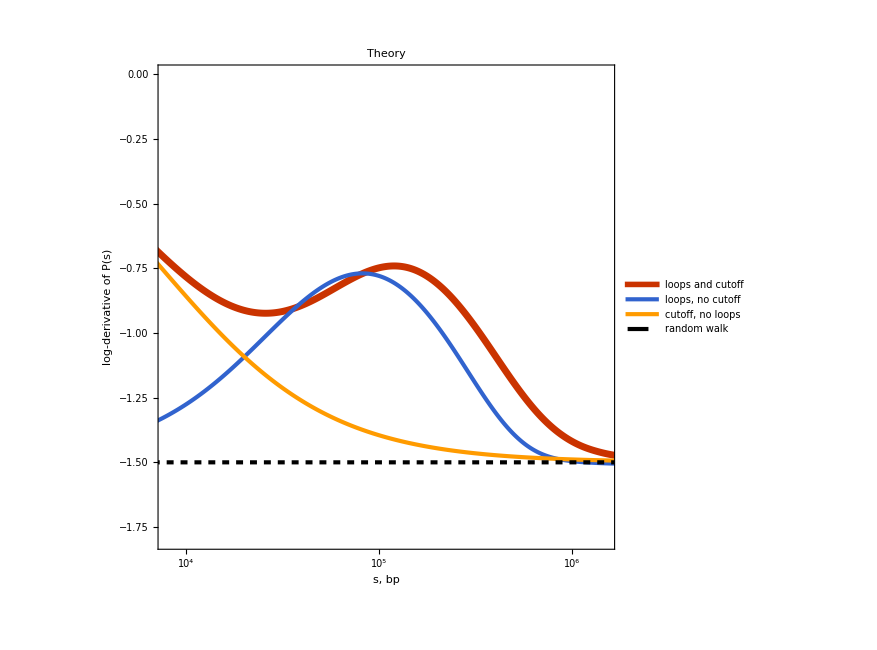

```mathematica
frameThickness=1.5;

tickFont=30;                   

Clear[yTicks];      

yTicks[min_,max_]:=Module[{ticks=Charting`ScaledTicks["Linear","Nice"][min,max]},ticks/. {p_,l_,r___}:>{p,Style[l,tickFont],r}];


log10Ticks[min_,max_]:=Module[{e=Range[Ceiling@Log10[min],Floor@Log10[max]]},Table[{10^i,Style[Superscript[10,i]]},{i,e}]];
myFrameStyle=Directive[Black,AbsoluteThickness[frameThickness], FontSize->50];
myTickStyle=Directive[Black,AbsoluteThickness[frameThickness/2],FontSize->50];

p4=ListLogLinearPlot[{logDerivative1,logDerivative2,logDerivative3,logDerivative4},Joined->True,InterpolationOrder->{3,3,3,1},PlotStyle->{Directive[AbsoluteThickness[5]],Directive[AbsoluteThickness[3]],Directive[AbsoluteThickness[3]],Directive[Black,Dashed,AbsoluteThickness[3]] },PlotTheme->{"Detailed","VibrantColor","LargeLabels","ThickLines"},PlotLegends->Placed[LineLegend[{Style["loops and cutoff",FontSize->36, FontFamily->"CMU Serif"],Style["loops, no cutoff",FontSize->36, FontFamily->"CMU Serif"],Style["cutoff, no loops",FontSize->36, FontFamily->"CMU Serif"],Style["random walk",FontSize->36, FontFamily->"CMU Serif"]}],{0.67,0.81}],GridLines->None,FrameTicksStyle->Directive[Black,Large],FrameLabel->{Text[Style["s, bp",FontSize->44,Black, FontFamily->"CMU Serif"]],Text[Style["log-derivative of P(s)",FontSize->44,Black, FontFamily->"CMU Serif"]]},ImageSize->650,AspectRatio->1,Ticks->{Table[{10^i,Superscript[10,i]},{i,4,5}],Automatic},FrameTicks->{{Automatic,None},{log10Ticks[10^4,10^6],None}   }, PlotRange->{{8*10^3,1.5* 10^6},{-1.8,0}},PlotLabel->Style["Theory",44,Black,FontFamily->"CMU Serif"],FrameStyle->myFrameStyle,FrameTicksStyle->myTickStyle]

pad={{80,20},{60,20}};
```